Matrix Usage Tutorial |

Pauli Operators and Related Vectorspaclet:Q3/tutorial/MatrixUsage#98311002 | Spin Operators and Related Vectorspaclet:Q3/tutorial/MatrixUsage#2084832021
Qubit Operators and Related Vectorspaclet:Q3/tutorial/MatrixUsage#1685553215 | Fermionic and Bosonic Operators and Related Vectorspaclet:Q3/tutorial/MatrixUsage#1798983883
Qudit Operators and Related Vectorspaclet:Q3/tutorial/MatrixUsage#168870253 | Dicke Systems (Cavity QED)paclet:Q3/tutorial/MatrixUsage#1016038474

Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol constructs the matrix representations of expressions involving operators or kets. It is one of the most frequently used functions in Q3.

Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol | Returns the matrix representation of expressions involving various types of operators or Kets.
Multiplypaclet:Q3/ref/MultiplyQ3 Package Symbol | Represents a non-commutative multiplication.
ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol | Converts the matrix representation to the corresponding operator or state-vector expression.

Functions related to Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol.

Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol applies to the whole Q3 application with the same usage syntax.

## Pauli Operators and Related Vectors

First, load the application.

```mathematica
<<Q3`
```

Consider an operator in terms of the Pauli operators on unlabelled qubits.

```mathematica
expr=Pauli[1,3]-2 Pauli[3,1]
```

X⊗Z-2 Z⊗X

Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol gives the matrix representation of the operator in the standard basis.

```mathematica
mat=Matrix[expr];
mat//MatrixForm
```

(0 | -2 | 1 | 0
-2 | 0 | 0 | -1
1 | 0 | 0 | 2
0 | -1 | 2 | 0)

You can check the basis used in the matrix representation by means of Basispaclet:Q3/ref/BasisQ3 Package Symbol.

```mathematica
bs=Basis[expr]
```

{0,0,0,1,1,0,1,1}

Here is another way of calculating the matrix representation -- the method of using Matrix is much more efficient.

```mathematica
mat2=Outer[Multiply,Dagger[bs],expr**bs];
mat2//MatrixForm
```

(0 | -2 | 1 | 0
-2 | 0 | 0 | -1
1 | 0 | 0 | 2
0 | -1 | 2 | 0)

```mathematica
mat-mat2//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol recovers the operator expression. For performance reasons, the output is expressed in terms of the lowering and raising operators.

```mathematica
new=ExpressionFor[mat]
```

-2 Z⊗X^+-2 Z⊗X^-+X^+⊗Z+X^-⊗Z

Convert it to a more traditional form using the Pauli X, Y, and Z operators.

```mathematica
Elaborate[new]
```

X⊗Z-2 Z⊗X

```mathematica
new-expr//Elaborate
```

0

Now consider a state vector in terms of Ketpaclet:Q3/ref/KetQ3 Package Symbol[…].

```mathematica
ket=Ket[1,0]-I Ket[0,1]
```

-ⅈ 0,1+1,0

For such an expression, Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol gives the column-vector representation of the state vector.

```mathematica
vec=Matrix[ket];
vec//MatrixForm
```

(0
-ⅈ
1
0)

Matrix also works for expression in Brapaclet:Q3/ref/BraQ3 Package Symbol[…].

```mathematica
Matrix[Dagger@ket]//Normal
```

{0,ⅈ,1,0}

```mathematica
ket=Ket[1,0]-I Ket[0,1]-3Ket[1,1]
```

-ⅈ 0,1+1,0-3 1,1

These are further examples.

```mathematica
vec0=TheKet[1,0]-I TheKet[0,1]-3TheKet[1,1];
vec0//Normal
vec1=Matrix[ket];
vec1//Normal
vec2=Matrix[ket];
vec2//Normal
```

{0,-ⅈ,1,-3}

{0,-ⅈ,1,-3}

{0,-ⅈ,1,-3}

## Qubit Operators and Related Vectors

```mathematica
<<Q3`
```

Let us now consider a system of labelled qubits.

```mathematica
Let[Qubit,S]
```

Here is an operator expression in terms of the Pauli operators on labelled qubits.

```mathematica
expr=CNOT[S[1],S[2]]**S[1,6]**CNOT[S[1],S[2]]//Elaborate
```

(S_1^xS_2^x)/(√2)+S_1^z/(√2)

The above expression corresponds to the following quatum circuit.

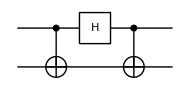

```mathematica
qc=QuantumCircuit[CNOT[S[1],S[2]],S[1,6],CNOT[S[1],S[2]]]
```

This gives the matrix representation in the standard basis.

```mathematica
mat=Matrix[expr];
mat//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | 1/(√2) | -1/(√2) | 0
1/(√2) | 0 | 0 | -1/(√2))

You can convert the quantum circuit directly to matrix as well.

```mathematica
Matrix[qc]//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | 1/(√2) | -1/(√2) | 0
1/(√2) | 0 | 0 | -1/(√2))

You can check the basis that is actually used for the matrix representation.

```mathematica
bs=Basis[expr];
bs//LogicalForm
```

{0_S_10_S_2,0_S_11_S_2,1_S_10_S_2,1_S_11_S_2}

You can construct the matrix representation using this basis.

```mathematica
mat2=Outer[Multiply,Dagger[bs],expr**bs];
mat2//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | 1/(√2) | -1/(√2) | 0
1/(√2) | 0 | 0 | -1/(√2))

The two results are the same as they should.

```mathematica
mat-mat2//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

For expressions in Ketpaclet:ref/Ket[<|…|>], the results are column vectors.

```mathematica
ket=expr**(Ket[]+Ket[S[1]->1])
Matrix[ket]//Normal
```

␣/(√2)-(1_S_1)/(√2)+(1_S_11_S_2)/(√2)+(1_S_2)/(√2)

{1/(√2),1/(√2),-1/(√2),1/(√2)}

```mathematica
bs=Basis[S@{1,2}];
Dagger[bs]**ket
```

{1/(√2),1/(√2),-1/(√2),1/(√2)}

## Qudit Operators and Related Vectors

```mathematica
<<Q3`
```

Here is an example for Qudit operators.

```mathematica
Let[Qudit,A]
```

```mathematica
op=A[1, 1 -> 2] + A[1, 2 -> 0] ** A[2, 1->0]
mat=Matrix[op];
mat // MatrixForm
```

(21)_1+(02)_1(01)_2

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
bs=Basis[A@{1,2}];
mat2=Outer[Multiply,Dagger[bs],op**bs];
mat2//MatrixForm
mat-mat2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ket=(1+op)**Ket[A[1]->2,A[2]->1]
vec=Matrix[ket,A@{1,2}];
vec//Normal
vec-Dagger[bs]**ket
```

␣+2_A_11_A_2

{1,0,0,0,0,0,0,1,0}

{0,0,0,0,0,0,0,0,0}

## Spin Operators and Related Vectors

```mathematica
<<Q3`
```

Let us now consider Spins (or general angular momenta).

```mathematica
Let[Spin,S,Spin->1]
```

```mathematica
H=MultiplyDot[S[1,{1,2,3}],S[2,{1,2,3}]]
```

S_1^xS_2^x+S_1^yS_2^y+S_1^zS_2^z

```mathematica
mat=Matrix[H];
mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
bs=Basis[S@{1,2}];
mat2=Outer[Multiply,Dagger[bs],H**bs];
mat2//MatrixForm
mat-mat2//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
mat3=Matrix[S[1,1]**S[1,3]];
mat3//MatrixForm
```

(0 | 0 | 0
1/(√2) | 0 | -1/(√2)
0 | 0 | 0)

Here is another example for Spin 1/2.

```mathematica
Let[Spin,S]
```

```mathematica
v=(3Ket[]+4Ket[S[1]->-1/2,S[2]->-1/2])/5
```

1/5 (3 ␣+4 (-1/2)_S_1(-1/2)_S_2)

```mathematica
vec1=v//Matrix;
vec1//Normal
vec0=3/5TheWignerKet[{1/2,1/2},{1/2,1/2}]+4/5TheWignerKet[{1/2,-1/2},{1/2,-1/2}];
vec0//Normal
vec0-vec1//Normal
```

{3/5,0,0,4/5}

{3/5,0,0,4/5}

{0,0,0,0}

Elaboratepaclet:Q3/ref/ElaborateQ3 Package Symbol converts dyad-type expressions (Ketpaclet:Q3/ref/KetQ3 Package Symbol[…]**Brapaclet:Q3/ref/BraQ3 Package Symbol[…] expressions) to the expression in terms of spin operators.

```mathematica
op=Dyad[v,v,S@{1,2}]
```

16/25 (-1/2)_S_1(-1/2)_S_2(-1/2)_S_1(-1/2)_S_2+12/25 (-1/2)_S_1(-1/2)_S_2(1/2)_S_1(1/2)_S_2+12/25 (1/2)_S_1(1/2)_S_2(-1/2)_S_1(-1/2)_S_2+9/25 (1/2)_S_1(1/2)_S_2(1/2)_S_1(1/2)_S_2

```mathematica
x=Elaborate[op]
```

1/4+24/25 S_1^xS_2^x-24/25 S_1^yS_2^y+S_1^zS_2^z-(7 S_1^z)/50-(7 S_2^z)/50

ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol can convert the matrix, too.

```mathematica
mat=Matrix[x];
mat//MatrixForm
```

(9/25 | 0 | 0 | 12/25
0 | 0 | 0 | 0
0 | 0 | 0 | 0
12/25 | 0 | 0 | 16/25)

```mathematica
y=ExpressionFor[mat,S@{1,2}]
```

1/4+S_1^zS_2^z+12/25 S_1^+S_2^++12/25 S_1^-S_2^--(7 S_1^z)/50-(7 S_2^z)/50

```mathematica
x-y//Elaborate
```

0

## Fermionic and Bosonic Operators and Related Vectors

```mathematica
<<Q3`
```

Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol can be used for many-body operators as well. Let us first consider Fermions.

```mathematica
Let[Fermion,c]
```

```mathematica
cc=c@{1,2,3}
```

{c_1,c_2,c_3}

```mathematica
Let[Real,t]
```

```mathematica
H=Q@cc-t PlusDagger@Hop@cc
```

c_1^†c_1+c_2^†c_2-t (c_1^†c_2+c_2^†c_1+c_2^†c_3+c_3^†c_2)+c_3^†c_3

```mathematica
bs=Basis[cc];
bs//LogicalForm
```

{0_c_10_c_20_c_3,0_c_10_c_21_c_3,0_c_11_c_20_c_3,0_c_11_c_21_c_3,1_c_10_c_20_c_3,1_c_10_c_21_c_3,1_c_11_c_20_c_3,1_c_11_c_21_c_3}

```mathematica
mat=Matrix[H];
mat//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -t | 0 | 0 | 0 | 0 | 0
0 | -t | 1 | 0 | -t | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | -t | 0 | 0
0 | 0 | -t | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -t | 0 | 2 | -t | 0
0 | 0 | 0 | 0 | 0 | -t | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

```mathematica
new=ExpressionFor[mat,cc]
```

-Graphics-

```mathematica
H-new//Garner
```

0

It can also be used for Bosons. However, it should be noted that only a finite number of basis elements are used.

```mathematica
Let[Boson,a,Bottom->0,Top->5]
```

```mathematica
Bottom[a]
Top[a]
```

0

5

```mathematica
aa=a@{1,2}
```

{a_1,a_2}

```mathematica
bs=Basis[aa];
bs//LogicalForm
```

{0_a_10_a_2,0_a_11_a_2,0_a_12_a_2,0_a_13_a_2,0_a_14_a_2,0_a_15_a_2,1_a_10_a_2,1_a_11_a_2,1_a_12_a_2,1_a_13_a_2,1_a_14_a_2,1_a_15_a_2,2_a_10_a_2,2_a_11_a_2,2_a_12_a_2,2_a_13_a_2,2_a_14_a_2,2_a_15_a_2,3_a_10_a_2,3_a_11_a_2,3_a_12_a_2,3_a_13_a_2,3_a_14_a_2,3_a_15_a_2,4_a_10_a_2,4_a_11_a_2,4_a_12_a_2,4_a_13_a_2,4_a_14_a_2,4_a_15_a_2,5_a_10_a_2,5_a_11_a_2,5_a_12_a_2,5_a_13_a_2,5_a_14_a_2,5_a_15_a_2}

```mathematica
Let[Real,t]
```

```mathematica
H=Q@aa-t PlusDagger@Hop@aa
```

a_1^†a_1-t (a_1^†a_2+a_2^†a_1)+a_2^†a_2

```mathematica
mat=Matrix[H];
MatrixForm[mat]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | -√2 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | -√3 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | -2 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | -√5 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -t | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -√2 t | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | -√2 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -√3 t | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | -2 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 t | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | -√6 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -√5 t | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | -2 √2 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | -√10 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -√2 t | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 t | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | -√3 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√6 t | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | -√6 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 √2 t | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | -3 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√10 t | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | -2 √3 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | -√15 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√3 t | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√6 t | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | -2 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 t | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | -2 √2 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 √3 t | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | -2 √3 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√15 t | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | -4 t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | -2 √5 t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 t | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 √2 t | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | -√5 t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 √3 t | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | -√10 t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 t | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | -√15 t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 √5 t | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | -2 √5 t | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | -5 t | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√5 t | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√10 t | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√15 t | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 √5 t | 0 | 0 | 0 | 0 | 8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 t | 0 | 0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10)

## Dicke Systems (Cavity QED)

```mathematica
<<Q3`
```

Consider bosonic modes and qubits interacting with each other.

```mathematica
Let[Boson,a,Top->2]
Let[Qubit,S]
bs=Basis[a,S];
bs//LogicalForm
```

{0_a0_S,0_a1_S,1_a0_S,1_a1_S,2_a0_S,2_a1_S}

```mathematica
H=Q[a]+(a+a^Dagger)**S[1]+S[3]/2
```

aS^x+a^†a+a^†S^x+S^z/2

```mathematica
mat=Matrix[H];
mat//MatrixForm
```

(1/2 | 0 | 0 | 1 | 0 | 0
0 | -1/2 | 1 | 0 | 0 | 0
0 | 1 | 3/2 | 0 | 0 | √2
1 | 0 | 0 | 1/2 | √2 | 0
0 | 0 | 0 | √2 | 5/2 | 0
0 | 0 | √2 | 0 | 0 | 3/2)

```mathematica
mat2=Outer[Multiply,Dagger[bs],H**bs ];
mat2//MatrixForm
mat-mat2//MatrixForm
```

(1/2 | 0 | 0 | 1 | 0 | 0
0 | -1/2 | 1 | 0 | 0 | 0
0 | 1 | 3/2 | 0 | 0 | √2
1 | 0 | 0 | 1/2 | √2 | 0
0 | 0 | 0 | √2 | 5/2 | 0
0 | 0 | √2 | 0 | 0 | 3/2)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

| Related Guides
▪Quantum Information Systems
▪Quantum Many-Body Systems
▪Quantum Spin Systems
▪Q3

| Related Tech Notes
▪Quantum Information Systems with Q3
▪Quantum Many-Body Systems with Q3
▪Quantum Spin Systems with Q3
▪Q3: Quick Start

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/